This notebook produces plots of the orbits generated by local complementation orbit up and including to 9 qubits, when isomorphic graphs are considered equal.

This work refers to the work “title goes here”, https://arxiv.org/abs/XXXX.XXXXX. Please see this work for assosciated documentation.

You can choose to import from .mx or .csv. Importing data from .mx is faster, but may not be possible on older versions of Mathematica. Importing from .csv is broken up into qubit number as it can be slow for large number of qubits. Feel free to just import the qubit number you are interested in.

## Load data

### Import data from ‘.csv’

#### Init

```mathematica
SetDirectory[NotebookDirectory[]];

(* Graph state display options*)
defcol=ColorData[97,"ColorList"][[7]];
graphsize=100;
vertexsize=0.30;
edgethickness =0.024;
impad=10;

(* precompiled import for csv *)
len4={2,4};
len5={2,6,10,3};
len6={2,6,4,16,10,25,5,5,21,16,2};
len7={2,6,6,16,10,10,16,44,44,14,66,10,10,21,26,36,28,72,114,56,92,57,33,9,46,9};
len8={2,6,6,16,4,16,10,16,44,16,44,10,25,44,44,26,120,66,14,25,120,72,172,10,10,10,21,10,44,66,26,26,28,44,132,114,72,72,198,56,28,10,56,66,72,63,66,176,76,194,352,154,542,300,214,14,66,66,6,57,28,17,72,87,114,372,70,264,542,156,174,542,262,802,117,10,37,36,7,103,46,170,74,340,254,433,476,28,9,39,46,208,298,24,267,4,22,46,28,7,51};
len9={2,6,6,16,6,16,10,10,16,44,16,44,16,16,44,44,44,44,26,120,10,44,44,66,26,66,120,14,44,120,26,44,120,72,120,112,328,72,66,120,328,72,328,174,18,196,464,10,16,10,21,16,44,66,26,36,26,44,26,28,44,132,114,5,44,72,44,28,72,132,26,120,372,72,72,75,56,28,56,44,26,66,132,114,176,120,28,120,72,66,120,372,352,76,542,56,176,352,154,120,176,42,72,76,72,154,372,352,196,542,300,76,120,352,72,328,194,198,194,484,542,300,984,66,46,74,328,208,352,968,542,300,984,1498,828,154,91,240,488,420,1428,498,5,36,132,66,75,66,114,14,204,24,57,28,87,72,132,26,72,372,114,372,114,112,542,264,94,87,132,198,176,46,198,264,372,1052,91,156,542,174,38,72,132,352,204,186,198,528,220,1052,296,300,754,754,76,194,188,352,28,220,372,372,1052,544,324,1008,312,1052,1052,1052,1056,1550,1534,220,186,1476,1498,924,763,156,308,98,542,272,300,984,754,3004,222,426,105,1436,704,1472,474,1508,1498,2104,4246,1328,28,37,21,89,14,46,57,186,170,142,170,74,340,76,204,198,102,542,306,320,484,782,38,36,204,220,198,372,542,1052,340,1052,1096,1594,94,192,178,476,542,596,920,3004,952,1544,806,202,1334,156,504,528,1052,462,340,192,542,542,476,1534,754,484,1564,952,1534,1550,1550,3004,1578,116,58,452,283,462,3088,908,399,2198,4306,4402,2270,2292,4378,2684,9,63,100,46,42,75,85,174,340,119,182,188,1578,460,220,166,1148,24,24,170,160,784,564,168,494,1536,1594,1610,1578,768,494,1568,476,1610,1626,124,484,1114,1628,814,1594,66,952,356,952,126,840,2214,4470,818,2262,8836,726,1129,1384,1398,305,844,4514,2336,476,153,27,70,46,162,170,276,340,220,494,1610,128,494,988,736,1348,227,608,1246,541,4580,4538,1384,2408,744,4594,4592,2366,344,870,119,115,99,30,269,538,238,68,772,1216,630,1414,672,836,4670,80,1464,1478,862,278,129,94,893,609,242,21,567};

fourLiorbits=Range[2];
fourLigraphlists=Table[0,{i,Range[2]},{j,len4[[i]]}];
four=4;

fiveLiorbits=Range[4];
fiveLigraphlists=Table[0,{i,Range[4]},{j,len5[[i]]}];
five=5;

sixLiorbits=Range[11];
sixLigraphlists=Table[0,{i,Range[11]},{j,len6[[i]]}];
six=6;

sevenLiorbits=Range[26];
sevenLigraphlists=Table[0,{i,Range[26]},{j,len7[[i]]}];
seven=7;

eightLiorbits=Range[101];
eightLigraphlists=Table[0,{i,Range[101]},{j,len8[[i]]}];
eight=8;

nineLiorbits=Range[440];
nineLigraphlists=Table[0,{i,Range[440]},{j,len9[[i]]}];
nine=9;
```

#### 4 qubit

```mathematica
fourLidat=ToString@Import["4qubitorbitsLi.csv"];
fourLidat=StringReplace[fourLidat,"("->"{"];
fourLidat=StringReplace[fourLidat,")"->"}"];
fourLidat=StringReplace[fourLidat,"-"->"->"];
fourLidat=ToExpression@fourLidat;

Do[
fourLiorbits[[i]]=Graph[
Range[fourLidatᵀ[[2]][[i]]],
fourLidatᵀ[[3]][[i]],EdgeLabels->Thread[fourLidatᵀ[[4]][[i]]ᵀ[[1]]->fourLidatᵀ[[4]][[i]]ᵀ[[2]]]
];
,{i,Length@fourLiorbits}];

Do[
fourLigraphlists[[i]][[j]]=Graph[
Range[four],
fourLidat[[i]][[5]][[j]]
];
fourLigraphlists[[i]][[j]]=UndirectedGraph[fourLigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@fourLidat},{j,Length@fourLidat[[i]][[5]]}];
```

#### 5 qubit

```mathematica
fiveLidat=ToString@Import["5qubitorbitsLi.csv"];
fiveLidat=StringReplace[fiveLidat,"("->"{"];
fiveLidat=StringReplace[fiveLidat,")"->"}"];
fiveLidat=StringReplace[fiveLidat,"-"->"->"];
fiveLidat=ToExpression@fiveLidat;

Do[
fiveLiorbits[[i]]=Graph[
Range[fiveLidatᵀ[[2]][[i]]],
fiveLidatᵀ[[3]][[i]],EdgeLabels->Thread[fiveLidatᵀ[[4]][[i]]ᵀ[[1]]->fiveLidatᵀ[[4]][[i]]ᵀ[[2]]]
];
,{i,Length@fiveLiorbits}];

Do[
fiveLigraphlists[[i]][[j]]=Graph[
Range[five],
fiveLidat[[i]][[5]][[j]]
];
fiveLigraphlists[[i]][[j]]=UndirectedGraph[fiveLigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@fiveLidat},{j,Length@fiveLidat[[i]][[5]]}];
```

#### 6 qubit

```mathematica
sixLidat=ToString@Import["6qubitorbitsLi.csv"];
sixLidat=StringReplace[sixLidat,"("->"{"];
sixLidat=StringReplace[sixLidat,")"->"}"];
sixLidat=StringReplace[sixLidat,"-"->"->"];
sixLidat=ToExpression@sixLidat;

Do[
sixLiorbits[[i]]=Graph[
Range[sixLidatᵀ[[2]][[i]]],
sixLidatᵀ[[3]][[i]],EdgeLabels->Thread[sixLidatᵀ[[4]][[i]]ᵀ[[1]]->sixLidatᵀ[[4]][[i]]ᵀ[[2]]]
];
,{i,Length@sixLiorbits}];

Do[
sixLigraphlists[[i]][[j]]=Graph[
Range[six],
sixLidat[[i]][[5]][[j]]
];
sixLigraphlists[[i]][[j]]=UndirectedGraph[sixLigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@sixLidat},{j,Length@sixLidat[[i]][[5]]}];
```

#### 7 qubit

```mathematica
sevenLidat=ToString@Import["7qubitorbitsLi.csv"];
sevenLidat=StringReplace[sevenLidat,"("->"{"];
sevenLidat=StringReplace[sevenLidat,")"->"}"];
sevenLidat=StringReplace[sevenLidat,"-"->"->"];
sevenLidat=ToExpression@sevenLidat;

Do[
sevenLiorbits[[i]]=Graph[
Range[sevenLidatᵀ[[2]][[i]]],
sevenLidatᵀ[[3]][[i]],EdgeLabels->Thread[sevenLidatᵀ[[4]][[i]]ᵀ[[1]]->sevenLidatᵀ[[4]][[i]]ᵀ[[2]]]
];
,{i,Length@sevenLiorbits}];

Do[
sevenLigraphlists[[i]][[j]]=Graph[
Range[seven],
sevenLidat[[i]][[5]][[j]]
];
sevenLigraphlists[[i]][[j]]=UndirectedGraph[sevenLigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@sevenLidat},{j,Length@sevenLidat[[i]][[5]]}];
```

#### 8 qubit (takes a few minutes)

```mathematica
eightLidat=Import["8qubitorbitsLi.csv"];
Print["Import successfull. Converting to string for processing.."];
eightLidat=ToString@eightLidat
Print["Successfull. Processing string.."];
eightLidat=StringReplace[eightLidat,"("->"{"];
eightLidat=StringReplace[eightLidat,")"->"}"];
eightLidat=StringReplace[eightLidat,"-"->"->"];
eightLidat=ToExpression@eightLidat;

Do[
eightLiorbits[[i]]=Graph[
Range[eightLidatᵀ[[2]][[i]]],
eightLidatᵀ[[3]][[i]],EdgeLabels->Thread[eightLidatᵀ[[4]][[i]]ᵀ[[1]]->eightLidatᵀ[[4]][[i]]ᵀ[[2]]]
];
,{i,Length@eightLiorbits}];

Do[
eightLigraphlists[[i]][[j]]=Graph[
Range[eight],
eightLidat[[i]][[5]][[j]]
];
eightLigraphlists[[i]][[j]]=UndirectedGraph[eightLigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@eightLidat},{j,Length@eightLidat[[i]][[5]]}];
```

#### 9 qubit (takes tens of minutes)

```mathematica
nineLidat=Import["9qubitorbitsLi.csv"];
Print["Import successfull. Converting to string for processing.."];
nineLidat=ToString@nineLidat
Print["Successfull. Processing string.."];
nineLidat=StringReplace[nineLidat,"("->"{"];
nineLidat=StringReplace[nineLidat,")"->"}"];
nineLidat=StringReplace[nineLidat,"-"->"->"];
nineLidat=ToExpression@nineLidat;

Do[
nineLiorbits[[i]]=Graph[
Range[nineLidatᵀ[[2]][[i]]],
nineLidatᵀ[[3]][[i]],EdgeLabels->Thread[nineLidatᵀ[[4]][[i]]ᵀ[[1]]->nineLidatᵀ[[4]][[i]]ᵀ[[2]]];
Print[i];];
,{i,Length@nineLiorbits}];

Do[
nineLigraphlists[[i]][[j]]=Graph[
Range[nine],
nineLidat[[i]][[5]][[j]]
];
nineLigraphlists[[i]][[j]]=UndirectedGraph[nineLigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
Print[i];
,{i,Length@nineLidat},{j,Length@nineLidat[[i]][[5]]}];
```

#### Initialise to one variable.

```mathematica
orbitsLi={{},{},{},fourLiorbits,fiveLiorbits,sixLiorbits,sevenLiorbits,eightLiorbits,nineLiorbits};
orbitsLigraphlist={{},{},{},fourLigraphlists,fiveLigraphlists,sixLigraphlists,sevenLigraphlists,nineLigraphlists};

ClearAll[fourLidat,fiveLidat,sixLidat,sevenLidat,eightLidat,nineLidat,fourLiorbits,fiveLiorbits,sixLiorbits,sevenLiorbits,eightLiorbits,nineLiorbits,fourLigraphlists,fiveLigraphlists,sixLigraphlists,sevenLigraphlists,nineLigraphlists];
```

### Import data from ‘.mx’

#### Import from Mathematica 11 ‘.mx’ (this may take 30s)

```mathematica
SetDirectory[NotebookDirectory[]];
orbitsLi=Import["orbitsLi.mx"];
orbitsLigraphlist=Import["orbitsLigraphlist.mx"];
```

## Functions

```mathematica
deleteIsoG1[gl_List]:=Module[{},DeleteDuplicates[gl,IsomorphicGraphQ]];

colourblender[one_,two_]:=Blend[{one,two},0.5]; 


plotOrbitLi[noqub_,myclass_]:=Module[{oedgelabels,theselabels,graphimgs,imsz,g1,graphlabelgraph,graphlabels,thisorbit},(* Sanitise graphs for printing *)
Do[orbitsLigraphlist[[noqub]][[myclass]][[i]] =Graph[orbitsLigraphlist[[noqub]][[myclass]][[i]],ImagePadding->0],{i,Length@orbitsLigraphlist[[noqub]][[myclass]]}];

(* Sanitise orbit edge labels for printing *)
theselabels=Sort@(List@@@PropertyValue[orbitsLi[[noqub]][[myclass]],EdgeLabels]);
oedgelabels={};
Do[If[theselabels[[i]][[1]][[1]]<=theselabels[[i]][[1]][[2]],AppendTo[oedgelabels ,{ theselabels[[i]][[1]][[1]]<->theselabels[[i]][[1]][[2]],theselabels[[i]][[2]]}]],{i,Length@theselabels}];
oedgelabels=Thread[oedgelabelsᵀ[[1]]->oedgelabelsᵀ[[2]]];

(* get images of each graph state to plot on the vertices of the orbit *)
graphimgs=Range@Length@orbitsLigraphlist[[noqub]][[myclass]];
imsz=100;
Do[
(* graph state vertices labelled? *)
If[graphsvertexlabelledQ,g1=Graph[orbitsLigraphlist[[noqub]][[myclass]][[i]],VertexLabels->Thread[Range[noqub]->Range[noqub]],VertexSize->svsize,EdgeStyle->sesize,VertexLabelStyle->Directive[Black,vertexlabelfontsize]];
g1=SetProperty[g1,VertexLabels->(#->Placed[#2,{0.59,0.4}]&@@@(VertexLabels/.Options[g1]))];
,
g1=Graph[orbitsLigraphlist[[noqub]][[myclass]][[i]],VertexSize->svsize,EdgeStyle->sesize];
];
graphimgs[[i]] = Show[{g1,
Graphics[{Directive[Black,Thickness[gcirclethickness]],Circle[{0,0},gpadding]}]},ImageSize->imsz]
,{i,Length@orbitsLigraphlist[[noqub]][[myclass]]}];
graphlabelgraph=Thread[Range[Length@orbitsLigraphlist[[noqub]][[myclass]]]->graphimgs];

(* compute graph state labels *)
If[graphslabelledQ ,
graphlabels= Table[i->"G"<>ToString[i],{i,Length@orbitsLigraphlist[[noqub]][[myclass]]}],
graphlabels=Thread[Range@Length@orbitsLigraphlist[[noqub]][[myclass]]->Table[None,{i,Length@orbitsLigraphlist[[noqub]][[myclass]]}]];
];


If[orbitedgeslabelledQ,
thisorbit=Graph[orbitsLi[[noqub]][[myclass]],VertexLabels->graphlabels,EdgeLabels->oedgelabels,VertexShape->graphlabelgraph,VertexSize->lvsize,EdgeStyle->lesize,EdgeLabelStyle->Directive[Black,edgefontsize],GraphLayout->"SpringEmbedding"];

If[graphslabelledQ ,thisorbit=SetProperty[thisorbit,VertexLabels->(#->Placed[#2,{0.51,0.29}]&@@@(VertexLabels/.Options[thisorbit]))];];
,
thisorbit=UndirectedGraph[orbitsLi[[noqub]][[myclass]],EdgeLabels->None,VertexShape->graphlabelgraph,VertexLabels->graphlabels,VertexSize->lvsize,EdgeStyle->lesize,EdgeLabelStyle->Directive[Black,edgefontsize],GraphLayout->"SpringEmbedding"];

If[graphslabelledQ ,thisorbit=SetProperty[thisorbit,VertexLabels->(#->Placed[#2,{0.51,0.29}]&@@@(VertexLabels/.Options[thisorbit]))];];
];

thisorbit];



plotOrbitMatrixLi[noqub_,myclass_]:=Module[{theselabels,oedgelabels,goodcolours,labels,colourlabel,mycolours,isocolours,isocolours2,gatheredisocols,isolens,isocount,colourisoadjmat,LCadj,isogroups,isomat,one,two,glo,glr,glos,bticks,arfaccumisolenssd,tickas,gl,btickstr,accumisolens,noedg,orbitadj,orbitlegend,dist,distp,distleg},


(* Sanitise graphs for printing *)
Do[orbitsLigraphlist[[noqub]][[myclass]][[i]] =Graph[orbitsLigraphlist[[noqub]][[myclass]][[i]],ImagePadding->0],{i,Length@orbitsLigraphlist[[noqub]][[myclass]]}];

(* Sanitise orbit edge labels for printing *)
theselabels=Sort@(List@@@PropertyValue[orbitsLi[[noqub]][[myclass]],EdgeLabels]);
oedgelabels={};
Do[If[theselabels[[i]][[1]][[1]]<=theselabels[[i]][[1]][[2]],AppendTo[oedgelabels ,{ theselabels[[i]][[1]][[1]]<->theselabels[[i]][[1]][[2]],theselabels[[i]][[2]]}]],{i,Length@theselabels}];
oedgelabels=Thread[oedgelabelsᵀ[[1]]->oedgelabelsᵀ[[2]]];


(*compute colour space*)
goodcolours=ColorData[97,"ColorList"];
labels=ToExpression[theselabelsᵀ[[2]]];

(*one colour per LC type (graph state vertex) *)
colourlabel=Flatten[labels/.{Thread[Range[15]->goodcolours]},1];
colourlabel={Sort@(List@@@PropertyValue[orbitsLi[[noqub]][[myclass]],EdgeLabels])ᵀ[[1]],colourlabel}ᵀ;

(*Isomorphic region colours*)
mycolours=Table[Hue[i/Length[orbitsLigraphlist[[noqub]][[myclass]]],satmod,brightmod],{i,Length@orbitsLigraphlist[[noqub]][[myclass]]}];
isocolours=mycolours;


(*Find regions of isomorphic graphs, set colour regions to 'isocolours'*)
Do[
Do[
If[SameQ[(Length@EdgeList@orbitsLigraphlist[[noqub]][[myclass]][[i]]),(Length@EdgeList@orbitsLigraphlist[[noqub]][[myclass]][[j]])],
isocolours[[j]]=mycolours[[i]];
]
,{j,Length@orbitsLigraphlist[[noqub]][[myclass]]}];
,{i,Length@orbitsLigraphlist[[noqub]][[myclass]]}];


(*define colours for regions of isomorphic graphs*)
isocolours2=Outer[colourblender,isocolours,isocolours];
gatheredisocols=isocolours2;
Do[
gatheredisocols[[i]]=Gather[isocolours2[[i]]],
{i,Length@orbitsLigraphlist[[noqub]][[myclass]]}];
isolens=Range[Length@gatheredisocols[[1]]];
Do[isolens[[i]]=Length@gatheredisocols[[1]][[i]],{i,Length@gatheredisocols[[1]]}];
isocount=Flatten[Table[j,{j,Length@isolens},{i,isolens[[j]]}]];


(*regions of same number of edges: 'gatheredisocols'*)
Do[
Do[gatheredisocols[[i]][[j]][[k]]=Blend[{gatheredisocols[[i]][[j]][[k]],Hue[0.95,0.0,1]},1*Abs[isocount[[i]]-j]/Length@gatheredisocols[[i]]],{k,Length@gatheredisocols[[i]][[j]]}];
,{i,Length@gatheredisocols},{j,Length@gatheredisocols[[i]]}];
Do[gatheredisocols[[i]]=Flatten[gatheredisocols[[i]]],{i,Length@orbitsLigraphlist[[noqub]][[myclass]]}];


(*varible to plot: 'colourisoadjmat'*)
colourisoadjmat=AdjacencyMatrix[orbitsLi[[noqub]][[myclass]]] //Normal;
Do[colourisoadjmat[[i]][[j]]=colourisoadjmat[[i]][[j]]+gatheredisocols[[i]][[j]],{i,Length@orbitsLigraphlist[[noqub]][[myclass]]},{j,Length@orbitsLigraphlist[[noqub]][[myclass]]}];
isogroups=colourisoadjmat;

Do[
one=colourlabel[[i]][[1]][[1]];
two=colourlabel[[i]][[1]][[2]];
If[
ToString[Head@colourlabel[[i]][[2]]]≠"List",
colourisoadjmat[[one]][[two]]=colourlabel[[i]][[2]],
colourisoadjmat[[one]][[two]]=colourlabel[[i]][[2]][[1]]]
,{i,Length@colourlabel}];



(*Make frame ticks*)
glo=Accumulate@isolens;
glr=glo;
glos=ToString/@glo;
accumisolens=Accumulate[isolens];
bticks=(Accumulate@isolens +Delete[ Flatten[PrependTo[accumisolens,0]],-1]) / 2;
noedg = Length/@EdgeList/@orbitsLigraphlist[[noqub]][[myclass]]//DeleteDuplicates;
btickstr=ToString/@noedg;
Do[
If[
Abs[bticks[[i+1]]-bticks[[i]]]<tickthresedge,
btickstr[[i]]=""
],{i,Length@bticks-1}];
Do[
If[
Abs[glo[[i+1]]-glo[[i]]]<tickthresno,
glos[[i]]=""
],{i,Length@glo-1}];
tickas={{glo+1/2,glos}ᵀ,{bticks+1/2,btickstr}ᵀ,None,{glo+1/2,glos}ᵀ};
gl={glr,Length@orbitsLigraphlist[[noqub]][[myclass]]-glr};



orbitadj=ArrayPlot[colourisoadjmat,
MaxPlotPoints->Length@AdjacencyMatrix[orbitsLi[[noqub]][[myclass]]]^2,
FrameStyle->AbsoluteThickness[myframethickness],
PlotRangePadding->0,
FrameLabel->{"Graph index","No.  Edges in graph","","Graph index"},
LabelStyle->{Black,FontFamily-> "Helvetica", FontSize-> myfontsize},
FrameTicks->tickas,
GridLines->gl,
FrameTicksStyle->Directive[Opacity[0],FontOpacity->1],
Method->{"GridLinesInFront"->True},
AspectRatio->1,
ImagePadding->40,
GridLinesStyle->Directive[Black,AbsoluteThickness[myframethickness/3]],
ImageSize->graphsize];

orbitlegend=TableForm[{Range[noqub],goodcolours[[1;;noqub]]}ᵀ];

dist=Table[0,{i,9},{j,Length/@orbitsLigraphlist[[i]]}];
dist[[noqub]][[myclass]]=GraphDistanceMatrix[orbitsLi[[noqub]][[myclass]]];

distp=MatrixPlot[dist[[noqub]][[myclass]],
MaxPlotPoints->Length@AdjacencyMatrix[orbitsLi[[noqub]][[myclass]]]^2,
FrameStyle->AbsoluteThickness[myframethickness],
PlotRangePadding->0,
FrameLabel->{"Graph index","No.  Edges in graph","","Graph index"},
LabelStyle->{Black,FontFamily-> "Helvetica", FontSize-> myfontsize},
FrameTicks->tickas,
GridLines->gl,
FrameTicksStyle->Directive[Opacity[0],FontOpacity->1],
Method->{"GridLinesInFront"->True},
AspectRatio->1,
GridLinesStyle->Directive[Black,AbsoluteThickness[myframethickness/3]],
ImageSize->graphsize,
ImagePadding->40,
ColorFunction->"SolarColors"];

distleg=BarLegend[{"SolarColors",{0,1+Max@dist[[noqub]][[myclass]]}},Max@dist[[noqub]][[myclass]],Method->{TicksStyle->Black,LabelStyle->{Black,FontFamily-> "Helvetica", FontSize-> myfontsize}} ];

{orbitadj,orbitlegend,distp,distleg}];
```

# Print unlabelled graph state orbits, L_i

## Which graph to plot?

#### Plot settings

```mathematica
sesize = Thickness[0.01];
lesize =Thickness[0.004];
svsize=0.4;
lvsize=0.4;
gcirclethickness=0.02;
gpadding=1.6;
edgefontsize=12;
vertexlabelfontsize=8;

(* Label edge vertices when printing orbit as a graph?*)
orbitedgeslabelledQ=True;   
graphslabelledQ=False;
graphsvertexlabelledQ=False;
```

#### Pick and display a graph state orbit

First graph in orbit is: -Graphics-

Number of graphs in Orbit is: 2

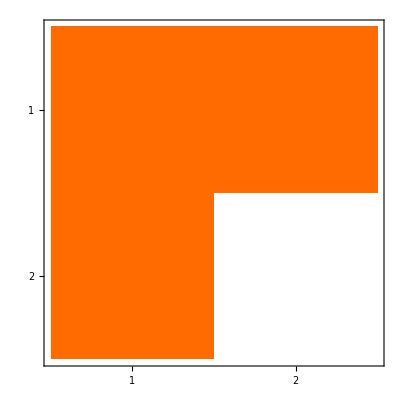
Adjacency matrix of orbit is: -Graphics-

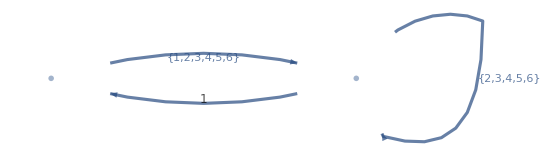

```mathematica
noqub=6;
myclass=1;

Print["First graph in orbit is: ",orbitsLigraphlist[[noqub]][[myclass]][[1]]]
Print["Number of graphs in Orbit is: ",Length@orbitsLigraphlist[[noqub]][[myclass]]]
Print["Adjacency matrix of orbit is: ",MatrixPlot@AdjacencyMatrix@orbitsLi[[noqub]][[myclass]]]

plotOrbitLi[noqub,myclass]
```

## Print unlabelled graph state orbits adjacency matrices, ordered and grouped by graph state isomorphism

#### Plot Settings

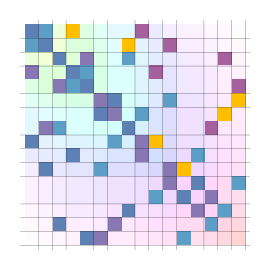
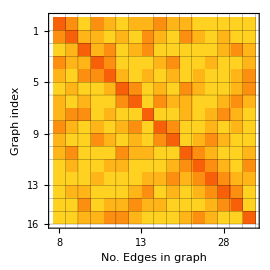
{-Graphics-,1 | RGBColor[0.368417, 0.506779, 0.709798]
2 | RGBColor[0.880722, 0.611041, 0.142051]
3 | RGBColor[0.560181, 0.691569, 0.194885]
4 | RGBColor[0.922526, 0.385626, 0.209179]
5 | RGBColor[0.528488, 0.470624, 0.701351]
6 | RGBColor[0.772079, 0.431554, 0.102387]
7 | RGBColor[0.363898, 0.618501, 0.782349]
8 | RGBColor[1, 0.75, 0]
9 | RGBColor[0.647624, 0.37816, 0.614037],-Graphics-,}

```mathematica
(*Adjust plot cosmetics*)
myframethickness=0.5;
myfontsize=10;
graphsize=270;

(*Adjust colour space for plots*)
satmod=0.17;
brightmod=1;

(*Difference in edge number required to be displayed on the plot*)
tickthresno=1;          (*in graph index*)
tickthresedge=1;     (*in edge number*)

plotOrbitMatrixLi[noqub,myclass]
```

# Exporter (used to generate .csv data)

## Four qubits

```mathematica
(*fourLiorbits=Table[StringReplace[ToString@EdgeList@orbitsLi[[4]][[i]]," -> "->"-"],{i,Length@orbitsLi[[4]]}];
Do[fourLiorbits[[i]]= StringReplace[fourLiorbits[[i]],"{"->"("];
fourLiorbits[[i]]= StringReplace[fourLiorbits[[i]],"}"->")"];
,{i,Length@fourLiorbits}] ;

fourorbitlabels=Table[StringReplace[ToString@Sort@(List@@@PropertyValue[orbitsLi[[4]][[i]],EdgeLabels])," -> "->"-"],{i,Length@orbitsLi[[4]]}];
Do[fourorbitlabels[[i]]= StringReplace[fourorbitlabels[[i]],"{"->"("];
fourorbitlabels[[i]]= StringReplace[fourorbitlabels[[i]],"}"->")"];
,{i,Length@fourorbitlabels}] ;

fourgraphs=Range@Length@orbitsLi[[4]];
Do[fourgraphs[[i]]=ToString[EdgeList/@orbitsLigraphlist[[4]][[i]]];
fourgraphs[[i]]= StringReplace[fourgraphs[[i]]," <-> "->"-"];
fourgraphs[[i]]= StringReplace[fourgraphs[[i]],"{"->"("];
fourgraphs[[i]]= StringReplace[fourgraphs[[i]],"}"->")"];
,{i,Length@orbitsLi[[4]]}] ;

fourqubitclasses={3,4};

fournoclasses=Table[Length@orbitsLigraphlist[[4]][[i]],{i,Length@orbitsLigraphlist[[4]]}];

fourLidats={fourqubitclasses,fournoclasses,fourLiorbits,fourorbitlabels,fourgraphs}ᵀ;

Export["4qubitorbitsLi.csv",fourLidats,"CSV"]*)
```

4qubitorbitsLi.csv

## Five qubits

```mathematica
(*fiveLiorbits=Table[StringReplace[ToString@EdgeList@orbitsLi[[5]][[i]]," -> "->"-"],{i,Length@orbitsLi[[5]]}];
Do[fiveLiorbits[[i]]= StringReplace[fiveLiorbits[[i]],"{"->"("];
fiveLiorbits[[i]]= StringReplace[fiveLiorbits[[i]],"}"->")"];
,{i,Length@fiveLiorbits}] ;

fiveorbitlabels=Table[StringReplace[ToString@Sort@(List@@@PropertyValue[orbitsLi[[5]][[i]],EdgeLabels])," -> "->"-"],{i,Length@orbitsLi[[5]]}];
Do[fiveorbitlabels[[i]]= StringReplace[fiveorbitlabels[[i]],"{"->"("];
fiveorbitlabels[[i]]= StringReplace[fiveorbitlabels[[i]],"}"->")"];
,{i,Length@fiveorbitlabels}] ;

fivegraphs=Range@Length@orbitsLi[[5]];
Do[fivegraphs[[i]]=ToString[EdgeList/@orbitsLigraphlist[[5]][[i]]];
fivegraphs[[i]]= StringReplace[fivegraphs[[i]]," <-> "->"-"];
fivegraphs[[i]]= StringReplace[fivegraphs[[i]],"{"->"("];
fivegraphs[[i]]= StringReplace[fivegraphs[[i]],"}"->")"];
,{i,Length@orbitsLi[[5]]}] ;

fivequbitclasses=Range[5,8];

fivenoclasses=Table[Length@orbitsLigraphlist[[5]][[i]],{i,Length@orbitsLigraphlist[[5]]}];

fiveLidats={fivequbitclasses,fivenoclasses,fiveLiorbits,fiveorbitlabels,fivegraphs}ᵀ;

Export["5qubitorbitsLi.csv",fiveLidats,"CSV"]*)
```

5qubitorbitsLi.csv

## Six qubits

```mathematica
(*sixLiorbits=Table[StringReplace[ToString@EdgeList@orbitsLi[[6]][[i]]," -> "->"-"],{i,Length@orbitsLi[[6]]}];
Do[sixLiorbits[[i]]= StringReplace[sixLiorbits[[i]],"{"->"("];
sixLiorbits[[i]]= StringReplace[sixLiorbits[[i]],"}"->")"];
,{i,Length@sixLiorbits}] ;

sixorbitlabels=Table[StringReplace[ToString@Sort@(List@@@PropertyValue[orbitsLi[[6]][[i]],EdgeLabels])," -> "->"-"],{i,Length@orbitsLi[[6]]}];
Do[sixorbitlabels[[i]]= StringReplace[sixorbitlabels[[i]],"{"->"("];
sixorbitlabels[[i]]= StringReplace[sixorbitlabels[[i]],"}"->")"];
,{i,Length@sixorbitlabels}] ;

sixgraphs=Range@Length@orbitsLi[[6]];
Do[sixgraphs[[i]]=ToString[EdgeList/@orbitsLigraphlist[[6]][[i]]];
sixgraphs[[i]]= StringReplace[sixgraphs[[i]]," <-> "->"-"];
sixgraphs[[i]]= StringReplace[sixgraphs[[i]],"{"->"("];
sixgraphs[[i]]= StringReplace[sixgraphs[[i]],"}"->")"];
,{i,Length@orbitsLi[[6]]}] ;

sixqubitclasses=Range[9,19];

sixnoclasses=Table[Length@orbitsLigraphlist[[6]][[i]],{i,Length@orbitsLigraphlist[[6]]}];

sixLidats={sixqubitclasses,sixnoclasses,sixLiorbits,sixorbitlabels,sixgraphs}ᵀ;

Export["6qubitorbitsLi.csv",sixLidats,"CSV"]*)
```

6qubitorbitsLi.csv

## Seven qubits

```mathematica
(*sevenLiorbits=Table[StringReplace[ToString@EdgeList@orbitsLi[[7]][[i]]," -> "->"-"],{i,Length@orbitsLi[[7]]}];
Do[sevenLiorbits[[i]]= StringReplace[sevenLiorbits[[i]],"{"->"("];
sevenLiorbits[[i]]= StringReplace[sevenLiorbits[[i]],"}"->")"];
,{i,Length@sevenLiorbits}] ;

sevenorbitlabels=Table[StringReplace[ToString@Sort@(List@@@PropertyValue[orbitsLi[[7]][[i]],EdgeLabels])," -> "->"-"],{i,Length@orbitsLi[[7]]}];
Do[sevenorbitlabels[[i]]= StringReplace[sevenorbitlabels[[i]],"{"->"("];
sevenorbitlabels[[i]]= StringReplace[sevenorbitlabels[[i]],"}"->")"];
,{i,Length@sevenorbitlabels}] ;

sevengraphs=Range@Length@orbitsLi[[7]];
Do[sevengraphs[[i]]=ToString[EdgeList/@orbitsLigraphlist[[7]][[i]]];
sevengraphs[[i]]= StringReplace[sevengraphs[[i]]," <-> "->"-"];
sevengraphs[[i]]= StringReplace[sevengraphs[[i]],"{"->"("];
sevengraphs[[i]]= StringReplace[sevengraphs[[i]],"}"->")"];
,{i,Length@orbitsLi[[7]]}] ;

sevenqubitclasses=Range[20,45];

sevennoclasses=Table[Length@orbitsLigraphlist[[7]][[i]],{i,Length@orbitsLigraphlist[[7]]}];

sevenLidats={sevenqubitclasses,sevennoclasses,sevenLiorbits,sevenorbitlabels,sevengraphs}ᵀ;

Export["7qubitorbitsLi.csv",sevenLidats,"CSV"]*)
```

7qubitorbitsLi.csv

## Eight qubits

```mathematica
(*eightLiorbits=Table[StringReplace[ToString@EdgeList@orbitsLi[[8]][[i]]," -> "->"-"],{i,Length@orbitsLi[[8]]}];
Do[eightLiorbits[[i]]= StringReplace[eightLiorbits[[i]],"{"->"("];
eightLiorbits[[i]]= StringReplace[eightLiorbits[[i]],"}"->")"];
,{i,Length@eightLiorbits}] ;

eightorbitlabels=Table[StringReplace[ToString@Sort@(List@@@PropertyValue[orbitsLi[[8]][[i]],EdgeLabels])," -> "->"-"],{i,Length@orbitsLi[[8]]}];
Do[eightorbitlabels[[i]]= StringReplace[eightorbitlabels[[i]],"{"->"("];
eightorbitlabels[[i]]= StringReplace[eightorbitlabels[[i]],"}"->")"];
,{i,Length@eightorbitlabels}] ;

eightgraphs=Range@Length@orbitsLi[[8]];
Do[eightgraphs[[i]]=ToString[EdgeList/@orbitsLigraphlist[[8]][[i]]];
eightgraphs[[i]]= StringReplace[eightgraphs[[i]]," <-> "->"-"];
eightgraphs[[i]]= StringReplace[eightgraphs[[i]],"{"->"("];
eightgraphs[[i]]= StringReplace[eightgraphs[[i]],"}"->")"];
,{i,Length@orbitsLi[[8]]}] ;

eightqubitclasses=Range[46,146];

eightnoclasses=Table[Length@orbitsLigraphlist[[8]][[i]],{i,Length@orbitsLigraphlist[[8]]}];

eightLidats={eightqubitclasses,eightnoclasses,eightLiorbits,eightorbitlabels,eightgraphs}ᵀ;

Export["8qubitorbitsLi.csv",eightLidats,"CSV"]*)
```

8qubitorbitsLi.csv

## Nine qubits

```mathematica
(*nineLiorbits=Table[StringReplace[ToString@EdgeList@orbitsLi[[9]][[i]]," -> "->"-"],{i,Length@orbitsLi[[9]]}];
Do[nineLiorbits[[i]]= StringReplace[nineLiorbits[[i]],"{"->"("];
nineLiorbits[[i]]= StringReplace[nineLiorbits[[i]],"}"->")"];
,{i,Length@nineLiorbits}] ;

nineorbitlabels=Table[StringReplace[ToString@Sort@(List@@@PropertyValue[orbitsLi[[9]][[i]],EdgeLabels])," -> "->"-"],{i,Length@orbitsLi[[9]]}];
Do[nineorbitlabels[[i]]= StringReplace[nineorbitlabels[[i]],"{"->"("];
nineorbitlabels[[i]]= StringReplace[nineorbitlabels[[i]],"}"->")"];
,{i,Length@nineorbitlabels}] ;

ninegraphs=Range@Length@orbitsLi[[9]];
Do[ninegraphs[[i]]=ToString[EdgeList/@orbitsLigraphlist[[9]][[i]]];
ninegraphs[[i]]= StringReplace[ninegraphs[[i]]," <-> "->"-"];
ninegraphs[[i]]= StringReplace[ninegraphs[[i]],"{"->"("];
ninegraphs[[i]]= StringReplace[ninegraphs[[i]],"}"->")"];
,{i,Length@orbitsLi[[9]]}] ;

ninequbitclasses=Range[147,586];

ninenoclasses=Table[Length@orbitsLigraphlist[[9]][[i]],{i,Length@orbitsLigraphlist[[9]]}];

nineLidats={ninequbitclasses,ninenoclasses,nineLiorbits,nineorbitlabels,ninegraphs}ᵀ;

Export["9qubitorbitsLi.csv",nineLidats,"CSV"]*)
```

9qubitorbitsLi.csv